## Prep

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/Dropbox/ISSAC/TORCH

```mathematica
imgSize=800;
```

## Data Vis

### Overall

```mathematica
dataRaw=Import["firstrun_decayed.dat"];
```

```mathematica
data1=Table[{dataRaw[[i]][[2]],dataRaw[[i]][[3]]},{i,1,Length@dataRaw}];
Grid@%
```

1 | 0.68299
2 | 4.1641×10^-20
3 | 2.3887×10^-15
4 | 0.13332
6 | 1.215×10^-30
7 | 1.0487×10^-21
9 | 2.1511×10^-6
10 | 3.6276×10^-15
11 | 1.0363×10^-13
12 | 1.6429×10^-19
13 | 0.00007994
14 | 9.316×10^-6
15 | 2.8572×10^-10
16 | 0.0011587
17 | 5.6751×10^-13
18 | 1.5001×10^-6
19 | 1.1336×10^-10
20 | 6.7451×10^-24
21 | 4.692×10^-25
22 | 5.469×10^-18
23 | 5.7561×10^-11
24 | 2.2664×10^-12
25 | 9.5792×10^-16
26 | 3.1926×10^-14
27 | 2.0004×10^-7
28 | 8.5969×10^-11
29 | 1.41×10^-9
30 | 1.3865×10^-10
31 | 1.7956×10^-9
32 | 1.2353×10^-8
33 | 1.5428×10^-8
34 | 5.3833×10^-7
36 | 5.0506×10^-10
35 | 5.3582×10^-9
37 | 8.0647×10^-8
36 | 5.8159×10^-29
38 | 1.3131×10^-9
40 | 2.4105×10^-9
39 | 1.1779×10^-7
40 | 1.6224×10^-29
41 | 2.462×10^-9
40 | 6.7532×10^-29
42 | 0.000090135
43 | 0.000087213
44 | 1.811×10^-6
46 | 0.000018788
48 | 0.00003539
45 | 2.3862×10^-7
46 | 6.5129×10^-29
47 | 5.3428×10^-7
48 | 1.0902×10^-28
49 | 5.6117×10^-6
50 | 4.9898×10^-7
50 | 1.8055×10^-29
51 | 0.000025785
50 | 6.0228×10^-29
52 | 0.000039439
53 | 1.9107×10^-6
54 | 6.4745×10^-7
55 | 1.1901×10^-6
54 | 7.4488×10^-29
56 | 0.000034007
57 | 1.9662×10^-7
58 | 0.0000192
59 | 8.4406×10^-6
58 | 7.3738×10^-29
60 | 6.1366×10^-8
61 | 0.000024525
62 | 0.000048233
64 | 0.000023249
63 | 1.4174×10^-6
65 | 3.7085×10^-7
64 | 7.8719×10^-29
66 | 7.6774×10^-6
67 | 3.0131×10^-6
68 | 2.0002×10^-7
70 | 5.6002×10^-6
69 | 5.721×10^-6
71 | 7.5673×10^-6
70 | 8.8033×10^-29
72 | 0.000058895
73 | 3.0104×10^-6
74 | 0.000015801
76 | 0.00071142
75 | 0.000046063
74 | 8.5358×10^-29
76 | 1.1466×10^-28
77 | 0.00003246
78 | 0.000028965
80 | 0.0019008
82 | 0.0044983
79 | 0.000087444
81 | 4.8924×10^-6
78 | 8.886×10^-29
80 | 1.1176×10^-28
82 | 1.7199×10^-28
83 | 0.000064128
84 | 4.2275×10^-6
86 | 0.00095955
85 | 0.00051888
87 | 7.5164×10^-6
84 | 9.8904×10^-29
86 | 1.9849×10^-28
87 | 2.0266×10^-28
88 | 0.00019507
89 | 0.000067559
90 | 1.6019×10^-6
91 | 0.000029058
92 | 0.00040725
94 | 0.00025246
96 | 4.165×10^-7
93 | 1.9351×10^-6
92 | 1.2513×10^-28
94 | 1.517×10^-28
95 | 0.00063299
96 | 4.1069×10^-29
97 | 0.000015553
98 | 1.1205×10^-6
100 | 0.00039456
96 | 1.2155×10^-28
98 | 1.5712×10^-28
99 | 0.000021353
100 | 2.0525×10^-28
101 | 3.9696×10^-6
102 | 0.0001385
104 | 1.5092×10^-6
103 | 0.00023826
102 | 1.258×10^-28
104 | 1.3742×10^-28
105 | 0.00035922
106 | 0.00013834
108 | 0.00040049
110 | 0.000031454
107 | 9.7862×10^-6
109 | 0.00011138
106 | 1.0734×10^-28
108 | 1.2226×10^-28
110 | 1.6028×10^-28
111 | 0.00023339
112 | 0.000021371
113 | 5.3654×10^-6
114 | 0.00059476
116 | 8.8535×10^-7
113 | 1.796×10^-28
115 | 3.2647×10^-6
112 | 1.2896×10^-28
114 | 1.7824×10^-28
115 | 1.7679×10^-28
116 | 2.1065×10^-28
117 | 0.000013749
118 | 2.0368×10^-6
119 | 0.00035786
120 | 0.000019754
122 | 0.00045312
124 | 0.001366
121 | 0.0001166
123 | 0.00061854
120 | 1.6697×10^-28
122 | 2.3299×10^-28
123 | 2.1389×10^-28
124 | 7.9821×10^-29
125 | 0.00066094
126 | 0.0016047
128 | 0.0025703
130 | 0.0022921
127 | 0.00014346
124 | 1.6037×10^-28
126 | 1.9993×10^-28
128 | 2.6224×10^-28
129 | 0.00039034
130 | 1.2217×10^-28
131 | 0.000030879
132 | 0.022867
134 | 0.092156
136 | 3.253×10^-6
133 | 0.014244
130 | 2.003×10^-28
132 | 2.0295×10^-28
134 | 2.8715×10^-28
135 | 0.000058223
136 | 2.219×10^-28
137 | 0.0097775
138 | 0.00014877
138 | 3.2114×10^-29
139 | 0.000043861
136 | 2.3288×10^-28
138 | 2.7856×10^-28
140 | 0.011495
142 | 2.4113×10^-8
141 | 2.2676×10^-6
142 | 4.9783×10^-28
143 | 1.4657×10^-6
144 | 1.3004×10^-7
145 | 2.2655×10^-6
146 | 1.7046×10^-7
148 | 4.5327×10^-7
150 | 8.8922×10^-7
144 | 2.1519×10^-28
147 | 4.9402×10^-6
148 | 2.9005×10^-28
149 | 7.734×10^-6
150 | 3.3692×10^-28
152 | 9.9795×10^-6
154 | 0.00068104
151 | 0.00052374
153 | 1.9279×10^-6
152 | 2.882×10^-28
154 | 2.8098×10^-28
155 | 2.0275×10^-6
156 | 4.2701×10^-7
157 | 0.000024706
158 | 0.00040963
160 | 0.00014126
159 | 2.4223×10^-6
156 | 2.2895×10^-28
158 | 2.3809×10^-28
160 | 2.8554×10^-28
161 | 0.00034322
162 | 4.5891×10^-7
163 | 3.491×10^-6
164 | 3.4282×10^-7
165 | 0.00041666
162 | 2.4202×10^-28
164 | 3.0008×10^-28
166 | 0.000044734
167 | 1.3175×10^-6
168 | 0.00042943
170 | 4.3464×10^-7
169 | 2.3617×10^-6
168 | 2.532×10^-28
170 | 3.2703×10^-28
171 | 6.5421×10^-6
172 | 0.00044556
173 | 2.4337×10^-6
174 | 0.00011971
176 | 4.0061×10^-7
175 | 0.0001946
176 | 4.3824×10^-29
174 | 2.8728×10^-28
176 | 3.9226×10^-28
177 | 0.000013518
178 | 0.0007517
179 | 1.7038×10^-6
180 | 1.0894×10^-7
180 | 4.8339×10^-29
181 | 5.3549×10^-7
180 | 3.7741×10^-28
182 | 1.3767×10^-7
183 | 6.5582×10^-7
184 | 5.3201×10^-8
186 | 1.7985×10^-6
185 | 0.00039136
187 | 3.0491×10^-6
184 | 3.1371×10^-28
186 | 3.693×10^-28
187 | 3.6359×10^-28
188 | 0.00027115
189 | 0.00039623
190 | 0.00041021
192 | 0.00037424
191 | 0.00030845
193 | 0.000033154
190 | 3.3682×10^-28
192 | 3.4299×10^-28
194 | 9.2824×10^-6
195 | 0.00009422
196 | 0.00018694
198 | 0.00011256
197 | 4.4657×10^-6
196 | 4.3689×10^-28
198 | 5.048×10^-28
199 | 9.2264×10^-8
200 | 0.000038225
201 | 7.8172×10^-9
202 | 7.6974×10^-10
204 | 6.6739×10^-10
203 | 7.7702×10^-9
205 | 5.0878×10^-9
204 | 3.6993×10^-28
206 | 6.0312×10^-10
207 | 4.8053×10^-9
208 | 4.2655×10^-10
209 | 6.3277×10^-6
232 | 3.1045×10^-7
235 | 1.4699×10^-8
238 | 4.866×10^-9

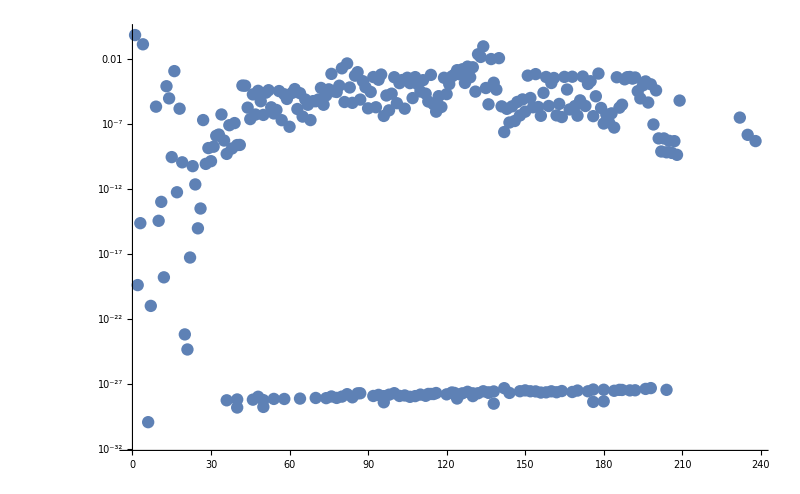

```mathematica
plt1=ListLogPlot[data1,ImageSize->imgSize]
```

Density plot.

```mathematica
densDat=Table[{dataRaw[[i]][[1]],dataRaw[[i]][[2]]-dataRaw[[i]][[1]],dataRaw[[i]][[3]]},{i,1,Length@dataRaw}];
Grid@%
```

1 | 0 | 0.68299
1 | 1 | 4.1641×10^-20
2 | 1 | 2.3887×10^-15
2 | 2 | 0.13332
3 | 3 | 1.215×10^-30
3 | 4 | 1.0487×10^-21
4 | 5 | 2.1511×10^-6
5 | 5 | 3.6276×10^-15
5 | 6 | 1.0363×10^-13
6 | 6 | 1.6429×10^-19
6 | 7 | 0.00007994
7 | 7 | 9.316×10^-6
7 | 8 | 2.8572×10^-10
8 | 8 | 0.0011587
8 | 9 | 5.6751×10^-13
8 | 10 | 1.5001×10^-6
9 | 10 | 1.1336×10^-10
10 | 10 | 6.7451×10^-24
10 | 11 | 4.692×10^-25
10 | 12 | 5.469×10^-18
11 | 12 | 5.7561×10^-11
12 | 12 | 2.2664×10^-12
12 | 13 | 9.5792×10^-16
12 | 14 | 3.1926×10^-14
13 | 14 | 2.0004×10^-7
14 | 14 | 8.5969×10^-11
14 | 15 | 1.41×10^-9
14 | 16 | 1.3865×10^-10
15 | 16 | 1.7956×10^-9
16 | 16 | 1.2353×10^-8
16 | 17 | 1.5428×10^-8
16 | 18 | 5.3833×10^-7
16 | 20 | 5.0506×10^-10
17 | 18 | 5.3582×10^-9
17 | 20 | 8.0647×10^-8
18 | 18 | 5.8159×10^-29
18 | 20 | 1.3131×10^-9
18 | 22 | 2.4105×10^-9
19 | 20 | 1.1779×10^-7
19 | 21 | 1.6224×10^-29
19 | 22 | 2.462×10^-9
20 | 20 | 6.7532×10^-29
20 | 22 | 0.000090135
20 | 23 | 0.000087213
20 | 24 | 1.811×10^-6
20 | 26 | 0.000018788
20 | 28 | 0.00003539
21 | 24 | 2.3862×10^-7
22 | 24 | 6.5129×10^-29
22 | 25 | 5.3428×10^-7
22 | 26 | 1.0902×10^-28
22 | 27 | 5.6117×10^-6
22 | 28 | 4.9898×10^-7
23 | 27 | 1.8055×10^-29
23 | 28 | 0.000025785
24 | 26 | 6.0228×10^-29
24 | 28 | 0.000039439
24 | 29 | 1.9107×10^-6
24 | 30 | 6.4745×10^-7
25 | 30 | 1.1901×10^-6
26 | 28 | 7.4488×10^-29
26 | 30 | 0.000034007
26 | 31 | 1.9662×10^-7
26 | 32 | 0.0000192
27 | 32 | 8.4406×10^-6
28 | 30 | 7.3738×10^-29
28 | 32 | 6.1366×10^-8
28 | 33 | 0.000024525
28 | 34 | 0.000048233
28 | 36 | 0.000023249
29 | 34 | 1.4174×10^-6
29 | 36 | 3.7085×10^-7
30 | 34 | 7.8719×10^-29
30 | 36 | 7.6774×10^-6
30 | 37 | 3.0131×10^-6
30 | 38 | 2.0002×10^-7
30 | 40 | 5.6002×10^-6
31 | 38 | 5.721×10^-6
31 | 40 | 7.5673×10^-6
32 | 38 | 8.8033×10^-29
32 | 40 | 0.000058895
32 | 41 | 3.0104×10^-6
32 | 42 | 0.000015801
32 | 44 | 0.00071142
33 | 42 | 0.000046063
34 | 40 | 8.5358×10^-29
34 | 42 | 1.1466×10^-28
34 | 43 | 0.00003246
34 | 44 | 0.000028965
34 | 46 | 0.0019008
34 | 48 | 0.0044983
35 | 44 | 0.000087444
35 | 46 | 4.8924×10^-6
36 | 42 | 8.886×10^-29
36 | 44 | 1.1176×10^-28
36 | 46 | 1.7199×10^-28
36 | 47 | 0.000064128
36 | 48 | 4.2275×10^-6
36 | 50 | 0.00095955
37 | 48 | 0.00051888
37 | 50 | 7.5164×10^-6
38 | 46 | 9.8904×10^-29
38 | 48 | 1.9849×10^-28
38 | 49 | 2.0266×10^-28
38 | 50 | 0.00019507
39 | 50 | 0.000067559
40 | 50 | 1.6019×10^-6
40 | 51 | 0.000029058
40 | 52 | 0.00040725
40 | 54 | 0.00025246
40 | 56 | 4.165×10^-7
41 | 52 | 1.9351×10^-6
42 | 50 | 1.2513×10^-28
42 | 52 | 1.517×10^-28
42 | 53 | 0.00063299
42 | 54 | 4.1069×10^-29
42 | 55 | 0.000015553
42 | 56 | 1.1205×10^-6
42 | 58 | 0.00039456
44 | 52 | 1.2155×10^-28
44 | 54 | 1.5712×10^-28
44 | 55 | 0.000021353
44 | 56 | 2.0525×10^-28
44 | 57 | 3.9696×10^-6
44 | 58 | 0.0001385
44 | 60 | 1.5092×10^-6
45 | 58 | 0.00023826
46 | 56 | 1.258×10^-28
46 | 58 | 1.3742×10^-28
46 | 59 | 0.00035922
46 | 60 | 0.00013834
46 | 62 | 0.00040049
46 | 64 | 0.000031454
47 | 60 | 9.7862×10^-6
47 | 62 | 0.00011138
48 | 58 | 1.0734×10^-28
48 | 60 | 1.2226×10^-28
48 | 62 | 1.6028×10^-28
48 | 63 | 0.00023339
48 | 64 | 0.000021371
48 | 65 | 5.3654×10^-6
48 | 66 | 0.00059476
48 | 68 | 8.8535×10^-7
49 | 64 | 1.796×10^-28
49 | 66 | 3.2647×10^-6
50 | 62 | 1.2896×10^-28
50 | 64 | 1.7824×10^-28
50 | 65 | 1.7679×10^-28
50 | 66 | 2.1065×10^-28
50 | 67 | 0.000013749
50 | 68 | 2.0368×10^-6
50 | 69 | 0.00035786
50 | 70 | 0.000019754
50 | 72 | 0.00045312
50 | 74 | 0.001366
51 | 70 | 0.0001166
51 | 72 | 0.00061854
52 | 68 | 1.6697×10^-28
52 | 70 | 2.3299×10^-28
52 | 71 | 2.1389×10^-28
52 | 72 | 7.9821×10^-29
52 | 73 | 0.00066094
52 | 74 | 0.0016047
52 | 76 | 0.0025703
52 | 78 | 0.0022921
53 | 74 | 0.00014346
54 | 70 | 1.6037×10^-28
54 | 72 | 1.9993×10^-28
54 | 74 | 2.6224×10^-28
54 | 75 | 0.00039034
54 | 76 | 1.2217×10^-28
54 | 77 | 0.000030879
54 | 78 | 0.022867
54 | 80 | 0.092156
54 | 82 | 3.253×10^-6
55 | 78 | 0.014244
56 | 74 | 2.003×10^-28
56 | 76 | 2.0295×10^-28
56 | 78 | 2.8715×10^-28
56 | 79 | 0.000058223
56 | 80 | 2.219×10^-28
56 | 81 | 0.0097775
56 | 82 | 0.00014877
57 | 81 | 3.2114×10^-29
57 | 82 | 0.000043861
58 | 78 | 2.3288×10^-28
58 | 80 | 2.7856×10^-28
58 | 82 | 0.011495
58 | 84 | 2.4113×10^-8
59 | 82 | 2.2676×10^-6
60 | 82 | 4.9783×10^-28
60 | 83 | 1.4657×10^-6
60 | 84 | 1.3004×10^-7
60 | 85 | 2.2655×10^-6
60 | 86 | 1.7046×10^-7
60 | 88 | 4.5327×10^-7
60 | 90 | 8.8922×10^-7
62 | 82 | 2.1519×10^-28
62 | 85 | 4.9402×10^-6
62 | 86 | 2.9005×10^-28
62 | 87 | 7.734×10^-6
62 | 88 | 3.3692×10^-28
62 | 90 | 9.9795×10^-6
62 | 92 | 0.00068104
63 | 88 | 0.00052374
63 | 90 | 1.9279×10^-6
64 | 88 | 2.882×10^-28
64 | 90 | 2.8098×10^-28
64 | 91 | 2.0275×10^-6
64 | 92 | 4.2701×10^-7
64 | 93 | 0.000024706
64 | 94 | 0.00040963
64 | 96 | 0.00014126
65 | 94 | 2.4223×10^-6
66 | 90 | 2.2895×10^-28
66 | 92 | 2.3809×10^-28
66 | 94 | 2.8554×10^-28
66 | 95 | 0.00034322
66 | 96 | 4.5891×10^-7
66 | 97 | 3.491×10^-6
66 | 98 | 3.4282×10^-7
67 | 98 | 0.00041666
68 | 94 | 2.4202×10^-28
68 | 96 | 3.0008×10^-28
68 | 98 | 0.000044734
68 | 99 | 1.3175×10^-6
68 | 100 | 0.00042943
68 | 102 | 4.3464×10^-7
69 | 100 | 2.3617×10^-6
70 | 98 | 2.532×10^-28
70 | 100 | 3.2703×10^-28
70 | 101 | 6.5421×10^-6
70 | 102 | 0.00044556
70 | 103 | 2.4337×10^-6
70 | 104 | 0.00011971
70 | 106 | 4.0061×10^-7
71 | 104 | 0.0001946
71 | 105 | 4.3824×10^-29
72 | 102 | 2.8728×10^-28
72 | 104 | 3.9226×10^-28
72 | 105 | 0.000013518
72 | 106 | 0.0007517
72 | 107 | 1.7038×10^-6
72 | 108 | 1.0894×10^-7
73 | 107 | 4.8339×10^-29
73 | 108 | 5.3549×10^-7
74 | 106 | 3.7741×10^-28
74 | 108 | 1.3767×10^-7
74 | 109 | 6.5582×10^-7
74 | 110 | 5.3201×10^-8
74 | 112 | 1.7985×10^-6
75 | 110 | 0.00039136
75 | 112 | 3.0491×10^-6
76 | 108 | 3.1371×10^-28
76 | 110 | 3.693×10^-28
76 | 111 | 3.6359×10^-28
76 | 112 | 0.00027115
76 | 113 | 0.00039623
76 | 114 | 0.00041021
76 | 116 | 0.00037424
77 | 114 | 0.00030845
77 | 116 | 0.000033154
78 | 112 | 3.3682×10^-28
78 | 114 | 3.4299×10^-28
78 | 116 | 9.2824×10^-6
78 | 117 | 0.00009422
78 | 118 | 0.00018694
78 | 120 | 0.00011256
79 | 118 | 4.4657×10^-6
80 | 116 | 4.3689×10^-28
80 | 118 | 5.048×10^-28
80 | 119 | 9.2264×10^-8
80 | 120 | 0.000038225
80 | 121 | 7.8172×10^-9
80 | 122 | 7.6974×10^-10
80 | 124 | 6.6739×10^-10
81 | 122 | 7.7702×10^-9
81 | 124 | 5.0878×10^-9
82 | 122 | 3.6993×10^-28
82 | 124 | 6.0312×10^-10
82 | 125 | 4.8053×10^-9
82 | 126 | 4.2655×10^-10
83 | 126 | 6.3277×10^-6
90 | 142 | 3.1045×10^-7
92 | 143 | 1.4699×10^-8
92 | 146 | 4.866×10^-9

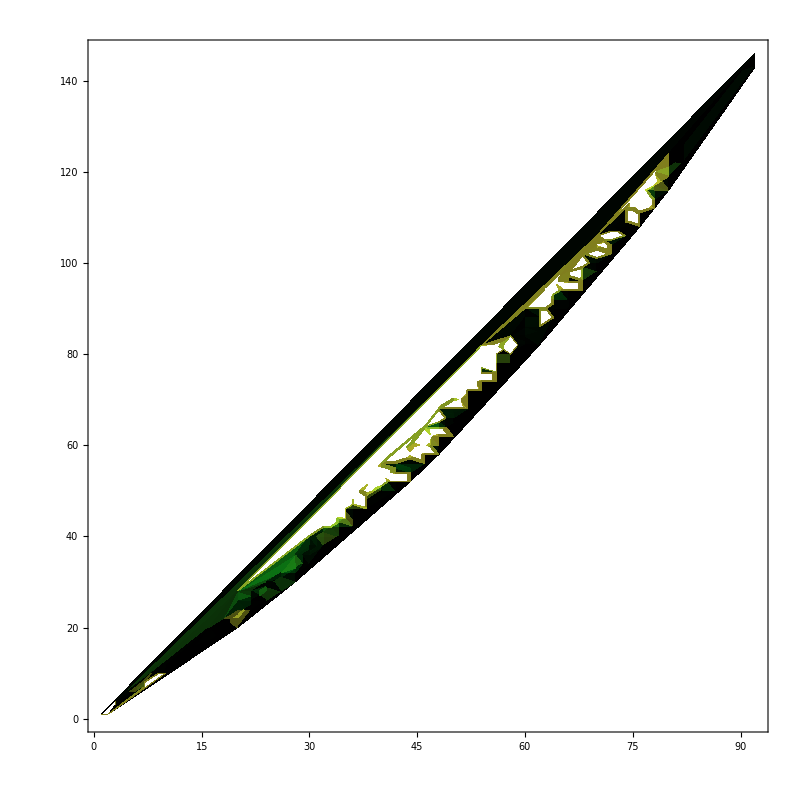

```mathematica
ListDensityPlot[densDat,ImageSize->imgSize,PlotPoints->25,InterpolationOrder->None,Frame->True,ColorFunction->ColorData["AvocadoColors"]]
```

```mathematica
list3DDat=Table[{dataRaw[[i]][[1]],dataRaw[[i]][[2]]-dataRaw[[i]][[1]],dataRaw[[i]][[3]]},{i,1,Length@dataRaw}];
Grid@%
```

### Evo

Time evolution of aboundance......